```mathematica
N[Pi 5^2]
```

78.5398

```mathematica
myRulePlot[rule_Integer]:= Rule[Tuples[{1,0},3],IntegerDigits[rule,2,8]
```

```mathematica
Rule[Tuples[{1,0},3],IntegerDigits[30,2,8]]
```

{{1,1,1},{1,1,0},{1,0,1},{1,0,0},{0,1,1},{0,1,0},{0,0,1},{0,0,0}}→{0,0,0,1,1,1,1,0}

```mathematica
Column/@Transpose[{Tuples[{1,0},3],IntegerDigits[30,2,8]}]
```

{{1,1,1}
0,{1,1,0}
0,{1,0,1}
0,{1,0,0}
1,{0,1,1}
1,{0,1,0}
1,{0,0,1}
1,{0,0,0}
0}

```mathematica
Map[Grid,Thread[Rule[Tuples[{1,0},3],IntegerDigits[30,2,8]]]/. {1->Black, 0->White}]
```

{Grid[{GrayLevel[0],GrayLevel[0],GrayLevel[0]}→GrayLevel[1]],Grid[{GrayLevel[0],GrayLevel[0],GrayLevel[1]}→GrayLevel[1]],Grid[{GrayLevel[0],GrayLevel[1],GrayLevel[0]}→GrayLevel[1]],Grid[{GrayLevel[0],GrayLevel[1],GrayLevel[1]}→GrayLevel[0]],Grid[{GrayLevel[1],GrayLevel[0],GrayLevel[0]}→GrayLevel[0]],Grid[{GrayLevel[1],GrayLevel[0],GrayLevel[1]}→GrayLevel[0]],Grid[{GrayLevel[1],GrayLevel[1],GrayLevel[0]}→GrayLevel[0]],Grid[{GrayLevel[1],GrayLevel[1],GrayLevel[1]}→GrayLevel[1]]}

```mathematica
Transpose[{Range[10],Range[10]}]
```

{{1,1},{2,2},{3,3},{4,4},{5,5},{6,6},{7,7},{8,8},{9,9},{10,10}}

```mathematica
Map[Framed,Map[ArrayPlot[#,ImageSize->Tiny]&,Transpose[{Tuples[{1,0},3], {0,#,0}&/@IntegerDigits[30,2,8]}]]]]]
```

-Graphics-

```mathematica
GraphicsRow[Map[Rasterize,Map[Grid,Transpose[{Tuples[{1,0},3], Map[{"",#,""}&,IntegerDigits[30,2,8]]}]/.{0->White, 1 -> Black}]],Frame -> All]
```

-Graphics-

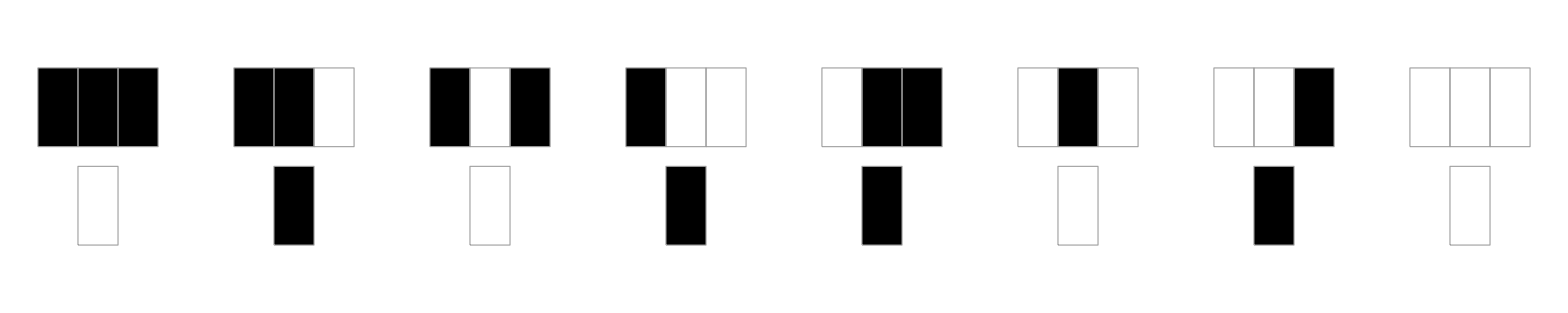

```mathematica
RulePlot[CellularAutomaton[90]]
```

```mathematica
myrl[rule_Integer]:=Rasterize[GraphicsRow[Map[GraphicsColumn,Transpose[{Map[ArrayPlot[{#},Mesh->All, ImageSize-> 30]&,Tuples[{1,0},3]],Map[Row[{"",#,""}]&,IntegerDigits[rule,2,8]/.{0->White, 1 -> Black}]}]],Frame -> All],ImageSize->Medium]
```

```mathematica
myrl[90]
```

-Graphics-

```mathematica
Show[%357,ImageSize->Medium]
```

-Graphics-

```mathematica
GraphicsRow[Map[Column,Transpose[{Map[ArrayPlot[{#},Mesh->All, ImageSize-> 30]&,Tuples[{1,0},3]],Map[ArrayPlot[{#},Frame-> False,ImageSize-> 30]&,Map[{0,ArrayPlot[{{#}}]&,0}&,IntegerDigits[30,2,8]]]}]],Frame->All]
```

-Graphics-

```mathematica
GraphicsRow[Map[Rasterize,Map[Column,Transpose[{Map[ArrayPlot[{#},Mesh->All, ImageSize-> 30]&,Tuples[{1,0},3]], Map[Row[{"",#,""}]&,IntegerDigits[30,2,8]]/.{0->White, 1 -> Black}}]]],Frame -> All]
```

-Graphics-

```mathematica
ArrayPlot[{{1}},ImageSize->15]
```

-Graphics-